```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

ObjToGraph::shdw: Symbol ObjToGraph appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

Global`

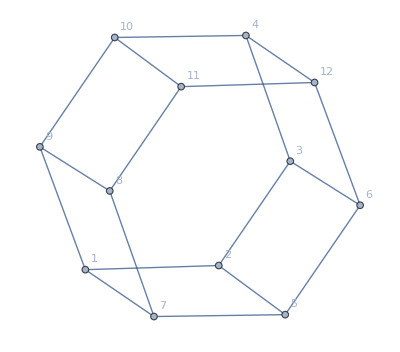

-Graphics3D-

```mathematica
ObjToGraph["data/cube.obj"]
PartitionObj["data/cube.obj"]
```

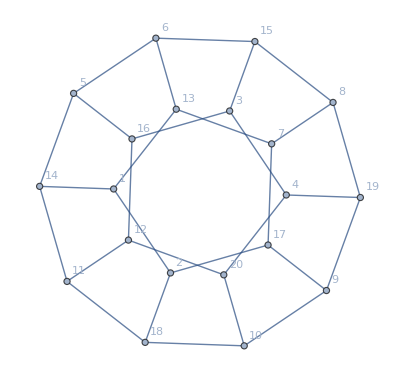

-Graphics3D-

```mathematica
ObjToGraph["data/icosahedron.obj"]
PartitionObj["data/icosahedron.obj"]
```

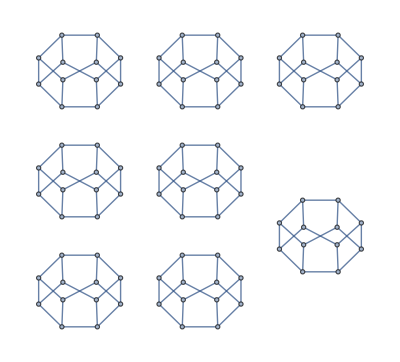

```mathematica
ObjToGraph["data/humanoid_tri.obj"]
```

```mathematica
ObjToGraph["data/bunny.obj"]
PartitionObj["data/bunny.obj"]
```

```mathematica
s="data/cube.obj";
data=ReadList[s,Word,RecordLists->True];
vertices=Map[ToExpression,Drop[#,1]&/@
				Select[data,First[#]=="v"&],{2}];
		If[data=!=$Failed,
			faces=Drop[#,1]&/@
				Select[data,First[#]=="f"&];
			If[vertices=!={}&&faces=!={},
				faces=If[DigitQ[faces[[1]][[1]]],
					Map[ToExpression,faces,{2}],
					Map[ToExpression[
						StringTake[#,StringPosition[#,"/"][[1]][[1]]-1]]&,
							faces,{2}]];
				FacesToGraph[faces,vertices],
				Print[s<>" does not seem to be an Obj file."]
			],
			Print[s<>" not found."]
		]
```

AddEdges[EmptyGraph[12],{{{2,1},EdgeWeight→1},{{7,1},EdgeWeight→1},{{9,1},EdgeWeight→1},{{3,2},EdgeWeight→1},{{5,2},EdgeWeight→1},{{4,3},EdgeWeight→1},{{6,3},EdgeWeight→1},{{10,4},EdgeWeight→1},{{12,4},EdgeWeight→1},{{6,5},EdgeWeight→1},{{7,5},EdgeWeight→1},{{12,6},EdgeWeight→1},{{8,7},EdgeWeight→1},{{9,8},EdgeWeight→1},{{11,8},EdgeWeight→1},{{10,9},EdgeWeight→1},{{11,10},EdgeWeight→1},{{12,11},EdgeWeight→1}}]

```mathematica
faces
vertices
```

{{1,7,5},{1,3,7},{1,4,3},{1,2,4},{3,8,7},{3,4,8},{5,7,8},{5,8,6},{1,5,6},{1,6,2},{2,6,8},{2,8,4}}

{{0.,0.,0.},{0.,0.,1.},{0.,1.,0.},{0.,1.,1.},{1.,0.,0.},{1.,0.,1.},{1.,1.,0.},{1.,1.,1.}}

```mathematica
elist =MeshToEdgeList[faces,vertices,1&]
g=Graph[Range[Length[faces]],Map[UndirectedEdge[#[[1]][[1]],#[[1]][[2]]]&, elist], 
VertexLabels->Automatic,
VertexWeight->Table[1/Length[faces], Length[faces]],EdgeWeight->Automatic]
```

{{{2,1},EdgeWeight→1},{{7,1},EdgeWeight→1},{{9,1},EdgeWeight→1},{{3,2},EdgeWeight→1},{{5,2},EdgeWeight→1},{{4,3},EdgeWeight→1},{{6,3},EdgeWeight→1},{{10,4},EdgeWeight→1},{{12,4},EdgeWeight→1},{{6,5},EdgeWeight→1},{{7,5},EdgeWeight→1},{{12,6},EdgeWeight→1},{{8,7},EdgeWeight→1},{{9,8},EdgeWeight→1},{{11,8},EdgeWeight→1},{{10,9},EdgeWeight→1},{{11,10},EdgeWeight→1},{{12,11},EdgeWeight→1}}

-Graphics-

```mathematica
UndirectedEdge[1,2]
```

1<->2

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
elist[[1]][[2]][[2]]
```

1

```mathematica
]
```